```mathematica
ClearAll["Global`*"]
```

#### version control

Earlier I used the the average orbital distance to calculate the maximum solar intensity, but now I am using the perihelion to calculate it.
3.2.1 The equations in the electrical system question 2 has been verified
3.2.2 The equations in the electrical system question 3 has been verified
3.2.3 Corrected the equation for the specific power at mars
added question E2 1

3.2.4 added to github
3.2.5 added question E2 2

# Spaceproject

## Functions

```mathematica
realQ[x_]:=Module[{},
If[
NumberQ[x]==False,
Print["Error: input to realQ is not a number"];
Return[];
];
If[Im[x]==0,Return[True],Return[False]];
];
```

## WP 3

Thermal control

## 2

```mathematica
σ = 5.67*10^-8;
T = 5780
q = σ T^4
r = 1392000*1000/2
p = q 4 π r^2
rm = 1.524 AU;
AU = 149597870700;
eMars = 0.093;
perihelion=rm (1-eMars);
qmax = p/(4 π perihelion^2)
```

5780

6.32841×10^7

696000000

3.85232×10^26

716.931

```mathematica
r
```

696000000

## 3

```mathematica
a = 0.15;
F = 1;
qam = qmax a F
```

107.54

## 6

```mathematica
rMars = 3.3899*10^6;
TMars = 210.1;
ϵMars = 1;
σ = 5.67*10^-8;
PMars = ϵMars 4 π rMars^2 σ TMars^4
```

1.5954×10^16

```mathematica
1*5.67*10^-8 4*3.1415*(3.3899*10^6)^2 210.1^4
```

1.59536×10^16

```mathematica
hOrbit = 500*1000;
aOrbit = rMars+hOrbit;
IROrbit = PMars/(4 π aOrbit^2)
```

83.9043

## 7

```mathematica
(*radiusSC = 1.65/2;*)
crossSection = π radiusSC^2;
surfaceArea = 4 π radiusSC^2;
σ=5.67*10^-8;
ISun = 716.931;
IAlb = 107.539;
IIR = 83.9;
(*QinternalHeat = 200;*)

α=1;
powerIn = α crossSection ISun+α crossSection IAlb+α crossSection IIR+QinternalHeat;

ϵ=1;
powerOut = ϵ σ surfaceArea Tsc^4;
ans7 = Tsc/.Solve[powerIn==powerOut,Tsc]//Flatten;
ans7=Select[Select[ans7,realQ@#&],#≥0&][[1]]
Print["Input power: ",powerIn,"\n","temperature: ",ans7]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Error: input to realQ is not a number

Error: input to realQ is not a number

Error: input to realQ is not a number

«1 more identical outputs»

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Input power: QinternalHeat+2853.73 radiusSC^2
temperature: {}⟦1⟧

```mathematica
Manipulate[Plot[1/(√radiusSC)1.9585356226300212 (1.9077048*^7+2.28387065*^8 radiusSC^2)^(1/4),{radiusSC,a,b},PlotRange->{0,250}],{{a,0},0,b-0.1},{{b,2},1,10}]
```

## 8

```mathematica
(*radiusSC = 1.65/2;*)
σ=5.67*10^-8;
ISun = 0; (*In the shadown*)
IAlb = 0; (*In the shadown*)
IIR = 83.9;
(*Qdiss = 0;*) (*no internal heat dissipation*)
crossSection = π radiusSC^2;
α=1;
QinSh = α crossSection ISun+α crossSection IAlb+α crossSection IIR+Qdiss;
surfaceArea = 4 π radiusSC^2;
ϵ=1;
powerOut = ϵ σ surfaceArea Tsc^4;
ans8 = Tsc/.Solve[
(QinSh/.{Qdiss->0,radiusSC->0.825})==(powerOut/.{Qdiss->0,radiusSC->0.825}),
Tsc]//Flatten;
ans8=Select[Select[ans8,realQ@#&],#≥0&][[1]];
Print[
"Input power: ",
QinSh/.{Qdiss->0,radiusSC->0.825},
"\n",
"temperature: ",
ans8]
```

Input power: 179.399
temperature: 138.685

## 9

```mathematica
aMars = 1.524;
eMars = 0.093;
(*radiusSC = 1.65/2;*)
Javg = 589.783;
α=1;
F=1;
ϵ=1;
albedo = 0.15;
JIR = 83.9;
(*Qdiss = 200;*)

crossSection = π radiusSC^2;
surfaceArea = 4 π radiusSC^2;
perihelion = aMars (1-eMars);
apohelion = aMars (1+eMars);

Jperi = Javg (aMars/perihelion)^2;
Japo = Javg (aMars/apohelion)^2;

JavgAlb = albedo Javg F;
JperiAlb = albedo Jperi F;
JapoAlb = albedo Japo F;
powerOut = ϵ σ surfaceArea Tsc^4;

QinAvg = α crossSection Javg + α crossSection JavgAlb + α crossSection JIR + Qdiss;
TAvg = (Tsc/.Solve[QinAvg==powerOut,Tsc]//Flatten);
TAvg = Select[Select[TAvg,realQ@#&],#≥0&][[1]];

QinPeri = α crossSection Jperi + α crossSection JperiAlb + α crossSection JIR + Qdiss;
TPeri = (Tsc/.Solve[QinPeri==powerOut,Tsc]//Flatten);
TPeri = Select[Select[TPeri,realQ@#&],#≥0&][[1]];

QinApo = α crossSection Japo + α crossSection JapoAlb + α crossSection JIR + Qdiss;
TApo = (Tsc/.Solve[QinApo==powerOut,Tsc]//Flatten);
TApo = Select[Select[TApo, realQ@#&],#≥ 0&][[1]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Error: input to realQ is not a number

Error: input to realQ is not a number

Error: input to realQ is not a number

«1 more identical outputs»

Part::partw: Part 1 of {} does not exist.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Error: input to realQ is not a number

Error: input to realQ is not a number

Error: input to realQ is not a number

«1 more identical outputs»

Part::partw: Part 1 of {} does not exist.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Error: input to realQ is not a number

Error: input to realQ is not a number

Error: input to realQ is not a number

«1 more identical outputs»

Part::partw: Part 1 of {} does not exist.

## 12

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

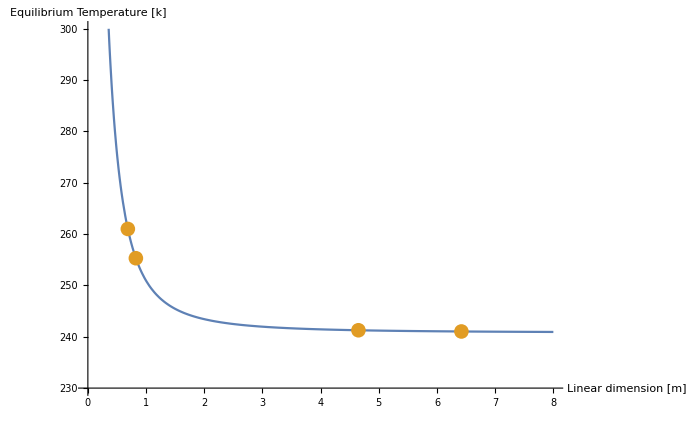

```mathematica
size = {0.687,0.825,4.65,6.42};
pwr = 2000/1.524^2/2;
plotFunction=(Tsc/.Solve[QinAvg==powerOut,Tsc])[[4]];
tempTable={
size,
plotFunction/.Qdiss->pwr/.radiusSC->size
}ᵀ;
Show[
Plot[
plotFunction/.Qdiss->pwr,
{radiusSC,0,8},
PlotRange->{230,300},
AxesLabel->{"Linear dimension [m]","Equilibrium Temperature [k]"},BaseStyle->{FontWeight->"Bold",FontSize->16},
ImageSize->700],
ListPlot[{{{0,0}},tempTable},PlotStyle->PointSize[0.015]]

]
```

```mathematica
pwr
```

430.556

Electrical subsystem

## #define

```mathematica
earthOrbit=1;
marsOrbit = 1.524;
```

## E1 1

```mathematica
radiusMars = 3390*10^3;
orbitHeight = 500*10^3;
orbitRadius = radiusMars+orbitHeight;
eclipseAngle = 2ArcSin[radiusMars/orbitRadius] 360/(2 π);
μMars = 4.282837×10^13;
orbitalPeriod = 2π √(orbitRadius^3/μMars);
(*Equations are verified*)
timeSpentIneclipse = eclipseAngle/360 orbitalPeriod;
marsYearInDays =686.971;
missionPeriodInSec = 686.971*24*60*60;
noOfEclipse = missionPeriodInSec/orbitalPeriod;
(*Equations are verified*)
```

## E1 2

```mathematica
powerForOtherSubsystem=200;
powerForPayload = 40;
totalPower = powerForOtherSubsystem+powerForPayload;
dayTimePathη = 0.8;
eclipsePathη = 0.6;
timeSpentInDay = orbitalPeriod-timeSpentIneclipse;
powerReqDay = totalPower/dayTimePathη;(*This would be the power the solar array would have to generate when the power flows in the path
Solar=>electrical stuff=>payload
*)


powerReqEclipse =totalPower/eclipsePathη; (*This would be the power the solar array would have to generate when the power flows in the path
Solar=>Electrical stuff=>battery management=>batter=>battery management=>electrical stuff=>payload
*)
energyReqDay = powerReqDay*timeSpentInDay;
energyReqEclipse = powerReqEclipse*timeSpentIneclipse;
totalEnergypPerOrbit = energyReqDay+energyReqEclipse;

powerSolarArray = totalEnergypPerOrbit/timeSpentInDay;

(*Equations are verified*)
```

## E1 3

```mathematica
powerDensityAt1AU=100 ;(*W/m^2*)
powerDensityAtMarsOrbit = powerDensityAt1AU( earthOrbit/marsOrbit)^2;
areaSolarArray = powerSolarArray/powerDensityAtMarsOrbit;
```

## E1 6

```mathematica
specificPowerSolarArrayAt1AU = 100;(*W/kg*)
specificPowerSolarArrayAtMars=specificPowerSolarArrayAt1AU *(earthOrbit/marsOrbit)^2;
massSolarArray = powerSolarArray/specificPowerSolarArrayAtMars
```

11.6864

## E2 1

```mathematica
specificPowerFuelCell = 100;(*W/kg*)
fuelCellReactantConsumptionRate = 0.5 ;(*kg/kWh*)
fuelCellPowerTransferη = rTGPowerTransferη;

fuelCellPowerMargin=rTGPowerMargin;

totalEnergyForMission = totalPower*missionPeriodInSec;
totalEnergyForMissionInkWh = totalEnergyForMission/(1000*3600)
```

3956.95

## E2 2

```mathematica
rTGPowerTransferη = 0.8;
rTGPowerMargin = 0.1;
powerRTGBOL=totalPower*(1+rTGPowerMargin)/rTGPowerTransferη;
plutoniumHalfLife = 90; (*years*)
missionPeriodInYears = marsYearInDays/365;
powerRTGEOL = powerRTGBOL(1/2)^(missionPeriodInYears/plutoniumHalfLife);
powerAvailableRTGAtEOL = powerRTGEOL*rTGPowerTransferη;
powerAvailableRTGAtBOL = powerRTGBOL*rTGPowerTransferη;
specificPowerRTG = 5;(*W/kg*)
massOfRTG = powerRTGBOL/specificPowerRTG;
```

#### Getting the relation for power distribution unit

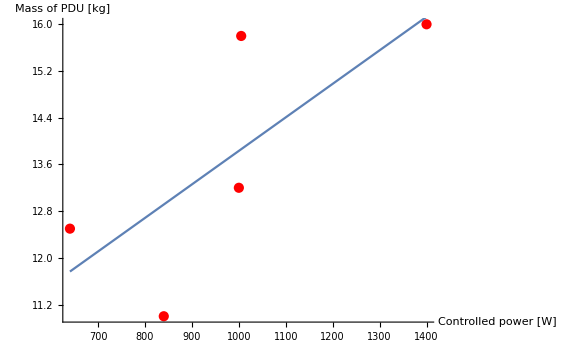

The relation for mass is: 8.09111+0.00574093 x

The mass of the PDU is: 9.98562kg
The RMS error in mass fit is: 1.29444kg

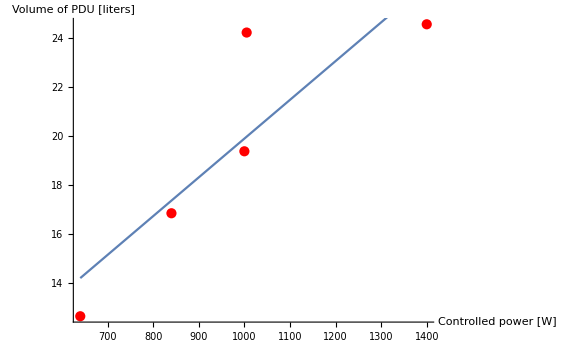

The relation for volume is: 4.06303+0.0158351 x

The volume of the PDU is: 9.28863 L
The RMS error in volume fit is: 2.18327 L

```mathematica
ClearAll[x];
massOfPDUs = {16,11,15.8,13.2,12.5};
volumeOfPDUs = {455 270 200,312 270 200,402 274 220,425 285 160,234 226 239}/(1000 1000);
powerDistributedByPDUs= 1000{1.4,0.84,1.005,1.000,0.64};

(*************************************************Fitting the mass data*)
PDUMassdataFit=FindFit[{powerDistributedByPDUs,massOfPDUs}ᵀ,b2+b1 x,{b1,b2},x];
Show[
ListPlot[{powerDistributedByPDUs,massOfPDUs}ᵀ,PlotStyle->Red,AxesLabel->{"Controlled power [W]","Mass of PDU [kg]"},BaseStyle->{FontWeight->"Bold",FontSize->15}],
Plot[Evaluate[b2+b1 x/. PDUMassdataFit],{x,640,1400}]
]

PDUMassdataRelation = b2+b1 x/. PDUMassdataFit;
PDUmass=PDUMassdataRelation/.x->330;
totalRTGSystemMass = massOfRTG+PDUmass;

distancesMass =ConstantArray[0,Length@massOfPDUs];
For[i=1,i<=Length@massOfPDUs,i++,
distancesMass[[i]] = massOfPDUs[[i]]-(PDUMassdataRelation/.x->powerDistributedByPDUs[[i]])
];
RMSErrorOfMassFit =RootMeanSquare[distancesMass];

Print["The relation for mass is: ",b2+b1 x/. PDUMassdataFit];
Print["The mass of the PDU is: ",PDUmass,"kg","\nThe RMS error in mass fit is: ",RMSErrorOfMassFit,"kg" ]
(*************************************************\Fitting the mass data*)


(*************************************************Fitting the volume data*)
(*Here a linear model of the form y = ax +b is used to fit the data. In the reader the model y = ax is used. This model gives a less RMS error*)
PDUVolumedataFit=FindFit[{powerDistributedByPDUs,volumeOfPDUs}ᵀ,b2+b1 x,{b1,b2},x];

Show[
ListPlot[{powerDistributedByPDUs,volumeOfPDUs}ᵀ,PlotStyle->Red,AxesLabel->{"Controlled power [W]","Volume of PDU [liters]"},BaseStyle->{FontWeight->"Bold",FontSize->15}],
Plot[Evaluate[b2+b1 x/. PDUVolumedataFit],{x,640,1400}]
]

PDUVolumedataRelation = b2+b1 x/. PDUVolumedataFit;
PDUVolume=PDUVolumedataRelation/.x->330;

distancesVolume =ConstantArray[0,Length@volumeOfPDUs];
For[i=1,i<=Length@volumeOfPDUs,i++,
distancesVolume[[i]] = volumeOfPDUs[[i]]-(PDUVolumedataRelation/.x->powerDistributedByPDUs[[i]])
];
RMSErrorOfVolumeFit =RootMeanSquare[distancesVolume];

Print["The relation for volume is: ",b2+b1 x/. PDUVolumedataFit];
Print["The volume of the PDU is: ",PDUVolume," L","\nThe RMS error in volume fit is: ",RMSErrorOfVolumeFit," L"]
(*************************************************\Fitting the volume data*)
```

#### Getting the relation for the power conditioning unit

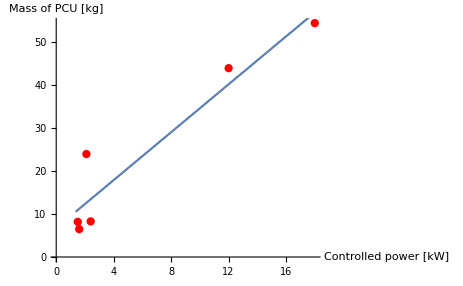

The relation for mass is: 6.76336+2.79042 x

The mass of the PCU is: 7.6842kg
The RMS error in mass fit is: 5.86303kg

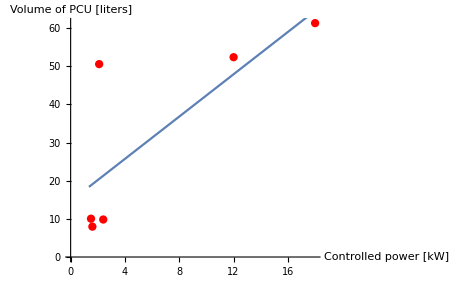

The relation for volume is: 14.6316+2.77207 x

The volume of the PCU is: 15.5464 L
The RMS error in volume fit is: 14.5318 L

```mathematica
ClearAll[x];
massOfPCUs = {8.3, 54.5,44,8.2,24,6.5};
volumeOfPCUs = {
267 233 158,
659 620 150,
563 620 150,
267 238 158,
540 520 180,
286 196 142
}/(1000 1000);
powerConditionedByPCUs= {2.4,18,12,1.5,2.1,1.6};

(*************************************************Fitting the mass data*)
PCUMassdataFit=FindFit[{powerConditionedByPCUs,massOfPCUs}ᵀ,b2+b1 x,{b1,b2},x];
Show[
ListPlot[{powerConditionedByPCUs,massOfPCUs}ᵀ,PlotStyle->Red,AxesLabel->{"Controlled power [kW]","Mass of PCU [kg]"},BaseStyle->{FontWeight->"Bold",FontSize->15}],
Plot[Evaluate[b2+b1 x/. PCUMassdataFit],
{x,
Min[powerConditionedByPCUs]0.9,
Max[powerConditionedByPCUs]1.1
}
]
]

PCUMassdataRelation = b2+b1 x/. PCUMassdataFit;
PCUmass=PCUMassdataRelation/.x-> 0.33;
totalRTGSystemMass = massOfRTG+PCUmass;

distancesMass =ConstantArray[0,Length@massOfPCUs];
For[i=1,i<=Length@massOfPCUs,i++,
distancesMass[[i]] = massOfPCUs[[i]]-(PCUMassdataRelation/.x->powerConditionedByPCUs[[i]])
];
RMSErrorOfMassFit =RootMeanSquare[distancesMass];

Print["The relation for mass is: ",b2+b1 x/. PCUMassdataFit];
Print["The mass of the PCU is: ",PCUmass,"kg","\nThe RMS error in mass fit is: ",RMSErrorOfMassFit,"kg" ]
(*************************************************\Fitting the mass data*)


(*************************************************Fitting the volume data*)
(*Here a linear model of the form y = ax +b is used to fit the data. In the reader the model y = ax is used. This model gives a less RMS error*)
PCUVolumedataFit=FindFit[{powerConditionedByPCUs,volumeOfPCUs}ᵀ,b2+b1 x,{b1,b2},x];

Show[
ListPlot[{powerConditionedByPCUs,volumeOfPCUs}ᵀ,PlotStyle->Red,AxesLabel->{"Controlled power [kW]","Volume of PCU [liters]"},BaseStyle->{FontWeight->"Bold",FontSize->15}],
Plot[Evaluate[b2+b1 x/. PCUVolumedataFit],
{x,
Min[powerConditionedByPCUs]0.9,
Max[powerConditionedByPCUs]1.1
}]
]

PCUVolumedataRelation = b2+b1 x/. PCUVolumedataFit;
PCUVolume=PCUVolumedataRelation/.x-> 0.33;

distancesVolume =ConstantArray[0,Length@volumeOfPCUs];
For[i=1,i<=Length@volumeOfPCUs,i++,
distancesVolume[[i]] = volumeOfPCUs[[i]]-(PCUVolumedataRelation/.x->powerConditionedByPCUs[[i]])
];
RMSErrorOfVolumeFit =RootMeanSquare[distancesVolume];

Print["The relation for volume is: ",b2+b1 x/. PCUVolumedataFit];
Print["The volume of the PCU is: ",PCUVolume," L","\nThe RMS error in volume fit is: ",RMSErrorOfVolumeFit," L"]
(*************************************************\Fitting the volume data*)
```

#### using the relations in the reader

```mathematica
powerDensityPDU = 50;(*W/l*)
powerDensityPCU = 192; (*W/l*)
volumeOfPDUReader = powerRTGBOL/powerDensityPDU;
volumeOfPCUReader = powerRTGBOL/powerDensityPCU;
Print["The volume of PDU using the reader's relation: ",volumeOfPDUReader,
"\nThe volume of PCU using the reader's relation: ",volumeOfPCUReader]
```

The volume of PDU using the reader's relation: 6.6
The volume of PCU using the reader's relation: 1.71875

```mathematica
330/192//N
```

1.71875

## Please note that eh variable x is cleared before this line